```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neutron/eth/ki/bin/trained_intnets

# Interaction Networks Permutation Invariance at Training AUC Experiments

## Quantised Networks

## Permutation Invariant Network - with summation layer

```mathematica
permInvPreds1=Partition[BinaryReadList["perm_invariant_1/plots_seed318/y_pred.dat","Real32"],5];
permInvPreds2=Partition[BinaryReadList["perm_invariant_1/plots_seed121/y_pred.dat","Real32"],5];
permInvPreds3=Partition[BinaryReadList["perm_invariant_1/plots_seed591/y_pred.dat","Real32"],5];
permInvPreds4=Partition[BinaryReadList["perm_invariant_1/plots_seed909/y_pred.dat","Real32"],5]; 
permInvPreds5=Partition[BinaryReadList["perm_invariant_1/plots_seed777/y_pred.dat","Real32"],5];
```

```mathematica
ΔpermInv0=Mean[Abs[permInvPreds1-permInvPreds2]];
ΔpermInv1=Mean[Abs[permInvPreds1-permInvPreds3]];
ΔpermInv2=Mean[Abs[permInvPreds1-permInvPreds4]];
ΔpermInv3=Mean[Abs[permInvPreds1-permInvPreds5]];
ΔpermInv4=Mean[Abs[permInvPreds2-permInvPreds3]];
ΔpermInv5=Mean[Abs[permInvPreds2-permInvPreds4]];
ΔpermInv6=Mean[Abs[permInvPreds2-permInvPreds5]];
ΔpermInv7=Mean[Abs[permInvPreds3-permInvPreds4]];
ΔpermInv8=Mean[Abs[permInvPreds3-permInvPreds5]];
ΔpermInv9=Mean[Abs[permInvPreds4-permInvPreds5]];
```

## Permutation Variant Network - without summation layer

```mathematica
permVarPreds1 = Partition[BinaryReadList["perm_variant_1/plots_seed318/y_pred.dat","Real32"],5];
permVarPreds2 = Partition[BinaryReadList["perm_variant_1/plots_seed121/y_pred.dat","Real32"],5];
permVarPreds3 = Partition[BinaryReadList["perm_variant_1/plots_seed591/y_pred.dat","Real32"],5];
permVarPreds4 = Partition[BinaryReadList["perm_variant_1/plots_seed909/y_pred.dat","Real32"],5];
permVarPreds5 = Partition[BinaryReadList["perm_variant_1/plots_seed777/y_pred.dat","Real32"],5];
```

```mathematica
ΔpermVar0=Mean[Abs[permVarPreds1-permVarPreds2]];
ΔpermVar1=Mean[Abs[permVarPreds1-permVarPreds3]];
ΔpermVar2=Mean[Abs[permVarPreds1-permVarPreds4]];
ΔpermVar3=Mean[Abs[permVarPreds1-permVarPreds5]];
ΔpermVar4=Mean[Abs[permVarPreds2-permVarPreds3]];
ΔpermVar5=Mean[Abs[permVarPreds2-permVarPreds4]];
ΔpermVar6=Mean[Abs[permVarPreds2-permVarPreds5]];
ΔpermVar7=Mean[Abs[permVarPreds3-permVarPreds4]];
ΔpermVar8=Mean[Abs[permVarPreds3-permVarPreds5]];
ΔpermVar9=Mean[Abs[permVarPreds4-permVarPreds5]];
```

## Plot the Δ

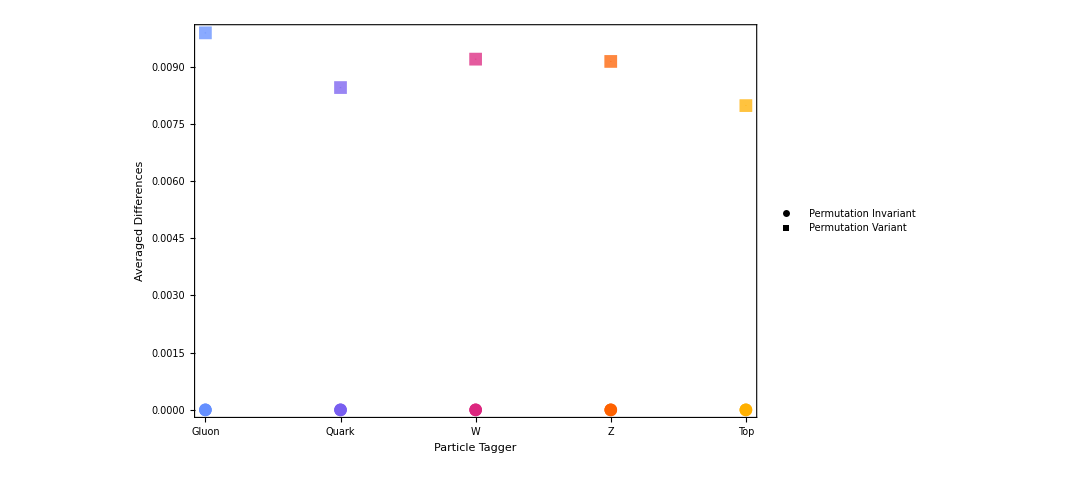

```mathematica
invariantΔ = {ΔpermInv0,ΔpermInv1,ΔpermInv2,ΔpermInv3,ΔpermInv4, ΔpermInv5, ΔpermInv6, ΔpermInv7, ΔpermInv8, ΔpermInv9};
variantΔ={ΔpermVar0,ΔpermVar1,ΔpermVar2,ΔpermVar3,ΔpermVar4,ΔpermVar5,ΔpermVar6,ΔpermVar7,ΔpermVar8,ΔpermVar9};

μinvariantΔ = Mean[invariantΔ];
σinvariantΔ = StandardDeviation[invariantΔ];

μvariantΔ = Mean[variantΔ];
σvariantΔ = StandardDeviation[variantΔ];

particleTypes = {1,2,3,4,5};
invariantData =Table[μinvariantΔ[[i]]± σinvariantΔ[[i]], {i,1,Length@μinvariantΔ}]; 
variantData = Table[μvariantΔ[[i]]± σvariantΔ[[i]], {i,1,Length@μvariantΔ}] ;

invariantPlotData = {#}&/@Transpose[{particleTypes, invariantData}];
variantPlotData = {#}&/@Transpose[{particleTypes, variantData}];

hexColors = {"#648FFF","#785EF0","#DC267F","#FE6100","#FFB000"};
hexColors = Map[RGBColor, hexColors];
lighterHexColors = {#, Opacity[0.5]}&/@hexColors;

invariantPlot = ListPlot[invariantPlotData, ImageSize->Large, PlotMarkers->{"•", 13}, PlotStyle->hexColors];
variantPlot = ListPlot[variantPlotData,ImageSize->800, PlotMarkers->{"■", 13}, PlotStyle->lighterHexColors];
plot = Show[variantPlot,invariantPlot, Frame->True, FrameStyle->Directive[18], FrameLabel->{"Particle Tagger","Averaged Differences"}, ImagePadding->80, FrameTicks->{{Automatic, Automatic}, {{{1, "Gluon"},{2, "Quark"}, {3, "W"}, {4,"Z"}, {5,"Top"}},Automatic}}, PlotRange->All, Axes->False];
legendPlot = Legended[plot,Placed[PointLegend[{Black, Black}, {"Permutation Invariant", "Permutation Variant"}, LegendMarkers->{{"•",15}, {"■",15}}, LabelStyle->15],{0.85,0.3}]]
```

```mathematica
Export["logits_invariance_qconv_8const.pdf",legendPlot]
```

logits_invariance_qconv_8const.pdf